The code to reproduce figures in the manuscript. 

Figure 2:

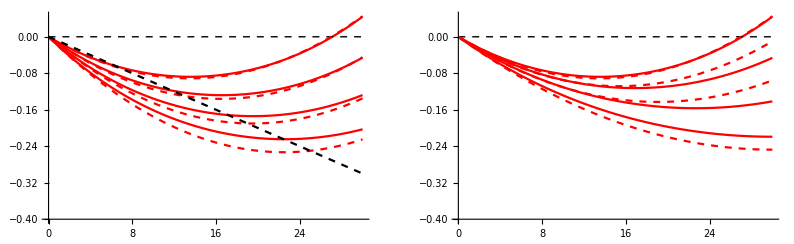

```mathematica
σexact[x_,f_,eb_,ew_,b_,s_]:=(1+s)^(x*(1-f)+(b-x*f))*(1+ew)^(Binomial[x*(1-f),2]+Binomial[b-x*f,2])* (1+eb)^((b-x*f)*(1-f)*x)/((1+s)^b*(1+ew)^Binomial[b,2])-1
σapp[x_,f_,eb_,ew_,b_,s_]:=(s*(x*(1-f)-f*x)+ ew*(Binomial[x*(1-f),2]-x*f/2*(2b-x*(1-f)-1))+eb*(b-x*f)*x*(1-f))
A := Plot[{σexact[x,0,-10^-4,10^-3,30,-10^-2],σexact[x,0,-10^-4,10^-3,60,-10^-2],σexact[x,0,-10^-4,10^-3,90,-10^-2],σexact[x,0,-10^-4,10^-3,120,-10^-2],0,σapp[x,0,-10^-4,10^-3,30,-10^-2],σapp[x,0,-10^-4,10^-3,60,-10^-2],σapp[x,0,-10^-4,10^-3,90,-10^-2],σapp[x,0,-10^-4,10^-3,120,-10^-2],σapp[x,0,0,0,120,-10^-2]},{x,0,30},
PlotStyle->{Red,Red,Red,Red,{Thin,Dashed,Black},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->Full];
B := Plot[{σexact[x,0,-10^-4,10^-3,30,-10^-2],σexact[x,0.1,-10^-4,10^-3,30,-10^-2],σexact[x,0.25,-10^-4,10^-3,30,-10^-2],σexact[x,0.5,-10^-4,10^-3,30,-10^-2],0,σapp[x,0,-10^-4,10^-3,30,-10^-2],σapp[x,0.1,-10^-4,10^-3,30,-10^-2],σapp[x,0.25,-10^-4,10^-3,30,-10^-2],σapp[x,0.5,-10^-4,10^-3,30,-10^-2]},{x,0,30},
PlotStyle->{Red,Red,Red,Red,{Thin,Dashed,Black},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red}},AxesOrigin->{0,-0.4}];
GraphicsRow[{A,B}]
```

```mathematica
Export["C:\\Users\\adagi\\Documents\\Wolfram Mathematica\\Figure 2_HaploInt_KeyResults.pdf",%6,"PDF"]
```

C:\Users\adagi\Documents\Wolfram Mathematica\Figure 2_HaploInt_KeyResults.pdf

Next, we have the diploid model supplementary figure:

```mathematica
wb[s_,ew_,b_]:=(1+s)^b*(1+ew)^Binomial[b,2]
σexact[s_,ew_,eb_,h_,a1_,a2_,xa_,xb_,b_]:= (1+s)^(b-xb)*(1+h*s)^(xb+xa)*(1+ew)^Binomial[b-xb,2]*(1+a1*ew)^(Binomial[xa,2]+Binomial[xb,2])*(1+a2*ew)^(xb*(b-xb))*(1+a1*eb)^(xb*xa)*(1+a2*eb)^(xa*(b-xb))/wb[s,ew,b]-1
additive:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,1*x,(1-1)*x,60],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.9*x,(1-0.9)*x,60],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.75*x,(1-0.75)*x,60],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.5*x,(1-0.5)*x,60],0},{x,0,30},
PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->""]
recessive:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,1*x,(1-1)*x,60],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,1*x,(1-0.9)*x,60],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,0.75*x,(1-0.75)*x,60],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,0.5*x,(1-0.5)*x,60],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->""]
dominant:=Plot[{σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,1*x,(1-1)*x,60],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,0.9*x,(1-0.9)*x,60],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,0.75*x,(1-0.75)*x,60],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,0.5*x,(1-0.5)*x,60],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->""]
r1:=GraphicsRow[{recessive,additive,dominant}]
additive2:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,x,0,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,x,0,60],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,x,0,90],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,x,0,120],0},{x,0,30},
PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->"Additive Epistasis"]
recessive2:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,x,0,30],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,x,0,60],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,x,0,90],σexact[-10^-2,10^-3,-10^-4,1/12,1/24,1/2,x,0,120],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->"Recessive Epistasis"]
dominant2:=Plot[{σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,x,0,30],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,x,0,60],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,x,0,90],σexact[-10^-2,10^-3,-10^-4,5/6,5/6,1/2,x,0,120],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.4},PlotRange->{{0,30},{-0.4,0.3}},PlotLabel->"Dominant Epistasis"]
r2:=GraphicsRow[{recessive2,additive2,dominant2}]
```

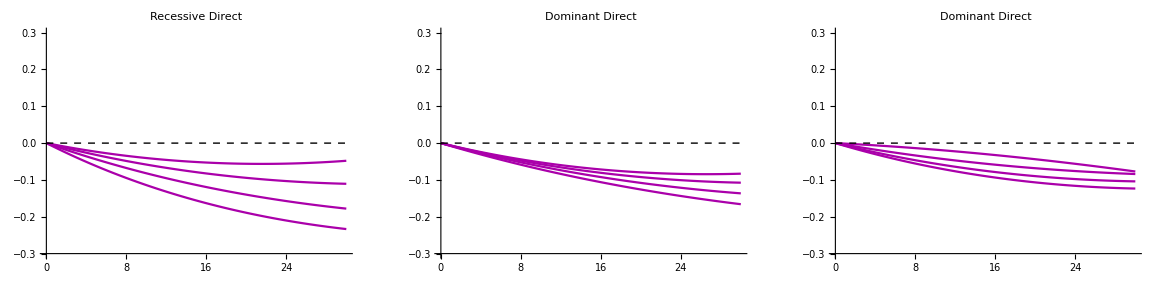

```mathematica
additive3:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,1*x,(1-1)*x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.9*x,(1-0.9)*x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.75*x,(1-0.75)*x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/2,0.5*x,(1-0.5)*x,30],0},{x,0,30},
PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.3},PlotRange->{{0,30},{-0.3,0.3}},PlotLabel->"Dominant Direct"]
recessive3:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/12,x,0,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/12,0.9x,0.1x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/12,0.75*x,0.25x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1/12,0.5x,0.5x,30],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.3},PlotRange->{{0,30},{-0.3,0.3}},PlotLabel->"Recessive Direct"]
dominant3:=Plot[{σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1,x,0,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1,0.9x,0.1x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1,0.75x,0.25x,30],σexact[-10^-2,10^-3,-10^-4,1/2,1/4,1,0.5x,0.5x,30],0},{x,0,30},PlotStyle->{Darker[Magenta],Darker[Magenta],Darker[Magenta],Darker[Magenta],{Thin,Dashed,Black}},AxesOrigin->{0,-0.3},PlotRange->{{0,30},{-0.3,0.3}},PlotLabel->"Dominant Direct"]
r3 = GraphicsRow[{recessive3,additive3, dominant3}]
```

```mathematica
GraphicsColumn[{r3,r2,r1}]
```

-Graphics-

Finally, we have the ternary plots. These are especially ugly code, but  it works! Using the exact calculation here takes forever, so buckle in.

```mathematica
myColors=Blend[{{0.1,Directive[RGBColor[0.653833829251545, 0., 0.44489204242008085],Opacity[1]]},{0,Directive[RGBColor[1., 1., 1.],Opacity[1]]},{-1,Directive[RGBColor[0., 0.7236285954070344, 0.9615320057984283],Opacity[1.]]}},#1]&
ColorData[1];
new = {{"myColorFunction", "", {}}, {"Gradients"}, 1, {-1, 0.1}, myColors, ""};
AppendTo[DataPaclets`ColorDataDump`colorSchemes,  new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,  "myColorFunction"];
```

Blend[{{0.1,Directive[RGBColor[0.653833829251545, 0., 0.44489204242008085],Opacity[1]]},{0,Directive[RGBColor[1., 1., 1.],Opacity[1]]},{-1,Directive[RGBColor[0., 0.7236285954070344, 0.9615320057984283],Opacity[1.]]}},#1]&

```mathematica
σexact2[fn_,fa_,fr_,x_,eb_,ew_,b_,s_] :=(1+s)^(x*(fn-fa)+b)*(1+ew)^(Binomial[x*(fn+fr),2]+Binomial[b-x*(fr+fa),2])* (1+eb)^((b-x*(fr+fa))*(fn+fr)*x)/((1+s)^b*(1+ew)^Binomial[b,2])-1
(*find the transformation function*)
tf=FindGeometricTransform[{{0,0,0},{1,0,0},{0.5,Sqrt[3]/2,0}},{{1,0,0},{0,1,0},{0,0,1}}][[2]];
(*function to make cartesian coordinates out of ternary coordinates*)
ccoords[pt_]:=tf[pt][[{1,2}]];
(*Create a set of coordinates that total 1*)
tcoords=DeleteCases[Tuples[Range[0,100,1],3],x_/;Total[x]!=100]/100;
Clear[tickPoints,tickMarks,tickLabels,axesLabels,region]
(*Now assuming 10 tick marks,not debugged with num=!=10*)
tickPoints[poly_,num_:10]:=Flatten[Map[(*Segment a line*)Table[poly[[#[[1]]]]+1/num i (poly[[#[[2]]]]-poly[[#[[1]]]]),{i,1,num}]&,(*Map over all faces,uses same number of ticks per face,not equidistant segments*)Table[{i,i+1},{i,1,2}]~Join~{{3,1}}],1];
(*Make tick marks angled such that the point along the ternary axes*)


tickMarks[poly_,num_:10]:=(GeometricTransformation[Line[#],ScalingTransform[0.25,#[[2]]-#[[1]],#[[1]]]]&/@Quiet@Drop[With[{list=tickPoints[region,10]},MapIndexed[{#1,Flatten[RotationTransform[-60 Degree,#1][list[[#2+1]]]]}&,list]],{10,-1,10}]);

(*Create tick labels for the ticks-note I do not use tick marks on the vertices*)
tickLabels[num_:10]:=Module[{t},t=Quiet@Drop[With[{list=tickPoints[region,num]},MapIndexed[Flatten[RotationTransform[-90 Degree,#1][tickPoints[region][[#2+1]]]]&,tickPoints[region]][[1;;-2]]],{num,-1,num}];
MapThread[Text[N@#1,#2]&,{Flatten@ConstantArray[Range[0+1/num,1-1/num,1/num],3],t}]];
(*Instead of vertex tick marks,I use a separate function and call these labels*)
axesLabels[a_,b_,c_]:={Text[a,{-0.01,0},{1,0}],Text[b,{1.01,0},{-1,0}],Text[c,{0.5,1.02 Sqrt[3]/2}]};
(*These functions require that a polygon is defined*)
region={{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}};
(* Generate all of the plots queietly*)
tfunc[a_,b_,c_]:=σexact2[a,b,c,20,-10^-5,10^-4,60,0 ];
div60x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,10^-4,60,0];
div60x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0.1,0,-.05,-0.1,-0.15},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,60,-10^-5,10^-4,60,0];
div60x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->{0.1,0,-.05,-0.1,-0.15},ContourLabels->True];

tfunc[a_,b_,c_]:=σexact2[a,b,c,20,-10^-5,10^-4,120,0];
div120x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,-0.15},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,10^-4,120,0];
div120x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.1,-0.2,-0.3,-0.4},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,60,-10^-5,10^-4,120,0];
div120x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->{0.05,0,-0.1,-0.2,-0.3,-0.4,-0.5},ContourLabels->True];

tfunc[a_,b_,c_]:=σexact2[a,b,c,20,-10^-5,10^-4,240,0];
div240x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.1,-0.2,-0.3},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,10^-4,240,0];
div240x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.1,-0.2,-0.3,-0.4,-0.5},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,60,-10^-5,10^-4,240,0];
div240x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->{0,-0.2,-0.4,-0.6},ContourLabels->True];
```

$Aborted

```mathematica
GraphicsColumn[{GraphicsRow[{div60x20,div60x40,div60x60}]
,GraphicsRow[{div120x20,div120x40,div120x60}]
,GraphicsRow[{div240x20,div240x40,div240x60}]
}]
```

-Graphics-

```mathematica
σapp[fn_,fa_,fr_,x_,eb_,ew_,b_,s_]:=s*(fn*x-fa*x)+ ew*(Binomial[x*(fn+fr),2]-x*(fa+fr)/2*(2b-x*(fa+fr)-1))+eb*(b-x*(fa+fr))*x*(fn+fr);
(*find the transformation function*)tf=FindGeometricTransform[{{0,0,0},{1,0,0},{0.5,Sqrt[3]/2,0}},{{1,0,0},{0,1,0},{0,0,1}}][[2]];
(*function to make cartesian coordinates out of ternary coordinates*)
ccoords[pt_]:=tf[pt][[{1,2}]];
(*Create a set of coordinates that total 1*)
tcoords=DeleteCases[Tuples[Range[0,100,1],3],x_/;Total[x]!=100]/100;
Clear[tickPoints,tickMarks,tickLabels,axesLabels,region]
(*Now assuming 10 tick marks,not debugged with num=!=10*)
tickPoints[poly_,num_:10]:=Flatten[Map[(*Segment a line*)Table[poly[[#[[1]]]]+1/num i (poly[[#[[2]]]]-poly[[#[[1]]]]),{i,1,num}]&,(*Map over all faces,uses same number of ticks per face,not equidistant segments*)Table[{i,i+1},{i,1,2}]~Join~{{3,1}}],1];
(*Make tick marks angled such that the point along the ternary axes*)


tickMarks[poly_,num_:10]:=(GeometricTransformation[Line[#],ScalingTransform[0.25,#[[2]]-#[[1]],#[[1]]]]&/@Quiet@Drop[With[{list=tickPoints[region,10]},MapIndexed[{#1,Flatten[RotationTransform[-60 Degree,#1][list[[#2+1]]]]}&,list]],{10,-1,10}]);

(*Create tick labels for the ticks-note I do not use tick marks on the vertices*)
tickLabels[num_:10]:=Module[{t},t=Quiet@Drop[With[{list=tickPoints[region,num]},MapIndexed[Flatten[RotationTransform[-90 Degree,#1][tickPoints[region][[#2+1]]]]&,tickPoints[region]][[1;;-2]]],{num,-1,num}];
MapThread[Text[N@#1,#2]&,{Flatten@ConstantArray[Range[0+1/num,1-1/num,1/num],3],t}]];
(*Instead of vertex tick marks,I use a separate function and call these labels*)
axesLabels[a_,b_,c_]:={Text[a,{-0.01,0},{1,0}],Text[b,{1.01,0},{-1,0}],Text[c,{0.5,1.02 Sqrt[3]/2}]};
(*These functions require that a polygon is defined*)
region={{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}};
(* Generate all of the plots queietly*)
tfunc[a_,b_,c_]:=σapp[a,b,c,20,-10^-5,10^-4,60,0];
div60x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-.05,-0.1,-0.15},ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,40,-10^-5,10^-4,60,0];
div60x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{-0.15,-.1,-0.05,0,0.05},ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,60,-10^-5,10^-4,60,0];
div60x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->{-0.15,-0.1,-0.05,0,0.05,0.1},ContourLabels->True];

tfunc[a_,b_,c_]:=σapp[a,b,c,20,-10^-5,10^-4,120,0];
div120x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{-0.2,-0.15,-0.1,-0.05,0},ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,40,-10^-5,10^-4,120,0];
div120x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->5,ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,60,-10^-5,10^-4,120,0];
div120x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->5,ContourLabels->True];

tfunc[a_,b_,c_]:=σapp[a,b,c,20,-10^-5,10^-4,240,0];
div240x20=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{-0.4,-0.3,-0.2,-0.1,0},ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,40,-10^-5,10^-4,240,0];
div240x40=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{-0.8,-0.6,-0.4,-0.2,0},ContourLabels->True];
tfunc[a_,b_,c_]:=σapp[a,b,c,60,-10^-5,10^-4,240,0];
div240x60=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,4],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends-> None,Contours->{0,-0.2,-0.4,-0.6,-0.8,-1},ContourLabels->True];
```

```mathematica
GraphicsColumn[{GraphicsRow[{div60x20,div60x40,div60x60}]
,GraphicsRow[{div120x20,div120x40,div120x60}]
,GraphicsRow[{div240x20,div240x40,div240x60}]
}]
```

-Graphics-

```mathematica
Export["C:\\Users\\adagi\\Documents\\Wolfram Mathematica\\SupFig_Ternary.pdf",%34,"PDF"]
```

C:\Users\adagi\Documents\Wolfram Mathematica\SupFig_Ternary.pdf

```mathematica
σexact2[fn_,fa_,fr_,x_,eb_,ew_,b_,s_] :=(1+s)^(x*(fn-fa)+b)*(1+ew)^(Binomial[x*(fn+fr),2]+Binomial[b-x*(fr+fa),2])* (1+eb)^((b-x*(fr+fa))*(fn+fr)*x)/((1+s)^b*(1+ew)^Binomial[b,2])-1
(*find the transformation function*)
tf=FindGeometricTransform[{{0,0,0},{1,0,0},{0.5,Sqrt[3]/2,0}},{{1,0,0},{0,1,0},{0,0,1}}][[2]];
(*function to make cartesian coordinates out of ternary coordinates*)
ccoords[pt_]:=tf[pt][[{1,2}]];
(*Create a set of coordinates that total 1*)
tcoords=DeleteCases[Tuples[Range[0,100,5],3],x_/;Total[x]!=100]/100;
Clear[tickPoints,tickMarks,tickLabels,axesLabels,region]
(*Now assuming 10 tick marks,not debugged with num=!=10*)
tickPoints[poly_,num_:10]:=Flatten[Map[(*Segment a line*)Table[poly[[#[[1]]]]+1/num i (poly[[#[[2]]]]-poly[[#[[1]]]]),{i,1,num}]&,(*Map over all faces,uses same number of ticks per face,not equidistant segments*)Table[{i,i+1},{i,1,2}]~Join~{{3,1}}],1];
(*Make tick marks angled such that the point along the ternary axes*)


tickMarks[poly_,num_:10]:=(GeometricTransformation[Line[#],ScalingTransform[0.25,#[[2]]-#[[1]],#[[1]]]]&/@Quiet@Drop[With[{list=tickPoints[region,10]},MapIndexed[{#1,Flatten[RotationTransform[-60 Degree,#1][list[[#2+1]]]]}&,list]],{10,-1,10}]);

(*Create tick labels for the ticks-note I do not use tick marks on the vertices*)
tickLabels[num_:10]:=Module[{t},t=Quiet@Drop[With[{list=tickPoints[region,num]},MapIndexed[Flatten[RotationTransform[-90 Degree,#1][tickPoints[region][[#2+1]]]]&,tickPoints[region]][[1;;-2]]],{num,-1,num}];
MapThread[Text[N@#1,#2]&,{Flatten@ConstantArray[Range[0+1/num,1-1/num,1/num],3],t}]];
(*Instead of vertex tick marks,I use a separate function and call these labels*)
axesLabels[a_,b_,c_]:={Text[a,{-0.01,0},{1,0}],Text[b,{1.01,0},{-1,0}],Text[c,{0.5,1.02 Sqrt[3]/2}]};
(*These functions require that a polygon is defined*)
region={{0,0},{1,0},{0.5,Sqrt[3]/2},{0,0}};
(* Generate all of the plots queietly*)
```

```mathematica
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,-10^-4,60,0 ];
figWithn4Betn5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,-10^-5,60,0 ];
figWithn5Betn5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.01,0.05,0.01},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,0,60,0 ];
figWith0Betn5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.005,-0.01,-0.02,-0.015},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,10^-5,60,0 ];
figWith5Betn5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-5,10^-4,60,0 ];
figWith4Betn5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];
```

```mathematica
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-4,-10^-4,60,0 ];
figWithn4Betn4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-4,-10^-5,60,0 ];
figWithn5Betn4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.01,0.05,0.01},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-4,0,60,0 ];
figWith0Betn4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-4,10^-5,60,0 ];
figWith5Betn4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,-10^-4,10^-4,60,0 ];
figWith4Betn4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
```

```mathematica
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,0,-10^-4,60,0 ];
figWithn4Bet0=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];tfunc[a_,b_,c_]:=σexact2[a,b,c,40,0,-10^-5,60,0 ];
figWithn5Bet0=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,0,0,60,0 ];
figWith0Bet0=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,0,10^-5,60,0 ];
figWith5Bet0=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,0,10^-4,60,0 ];
figWith4Bet0=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
```

```mathematica
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-4,-10^-4,60,0 ];
figWithn4Bet4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-4,10^-5,60,0 ];
figWithn5Bet4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.01,0.05,0.01},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-4,0,60,0 ];
figWith0Bet4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-4,10^-5,60,0 ];
figWith5Bet4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-4,10^-4,60,0 ];
figWith4Bet4=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];

tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-5,-10^-4,60,0 ];
figWithn4Bet5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->{0,-0.05,-0.1,0.05,0.1},ContourLabels->True];tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-5,-10^-5,60,0 ];
figWithn5Bet5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-5,0,60,0 ];
figWith0Bet5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-5,10^-5,60,0 ];
figWith5Bet5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
tfunc[a_,b_,c_]:=σexact2[a,b,c,40,10^-5,10^-4,60,0 ];
figWith4Bet5=ListContourPlot[Partition[Flatten@Transpose[{ccoords/@tcoords,tfunc@@@tcoords}],3],ColorFunctionScaling->False,ColorFunction->ColorData["myColorFunction"],Epilog->{Line@region,Black,Quiet@tickMarks[region,10],tickLabels[],axesLabels["","",""]},Frame->None,PlotRange->{{-0.1,1.1},{-0.1,1.1}},PlotLegends->None,Contours->4,ContourLabels->True];
```

```mathematica
GraphicsColumn[{GraphicsRow[{figWithn4Bet4,figWithn5Bet4,figWith0Bet4,figWith5Bet4,figWith4Bet4}],GraphicsRow[{figWithn4Bet5,figWithn5Bet5,figWith0Bet5,figWith5Bet5,figWith4Bet5}],GraphicsRow[{figWithn4Bet0,figWithn5Bet0,figWith0Bet0,figWith5Bet0,figWith4Bet0}],GraphicsRow[{figWithn4Betn5,figWithn5Betn5,figWith0Betn5,figWith5Betn5,figWith4Betn5}],GraphicsRow[{figWithn4Betn4,figWithn5Betn4,figWith0Betn4,figWith5Betn4,figWith4Betn4}]}]
```

-Graphics-